```mathematica
Exit[]
```

```mathematica
$Assumptions=t>0&&a>0&&b>0
```

t>0&&a>0&&b>0

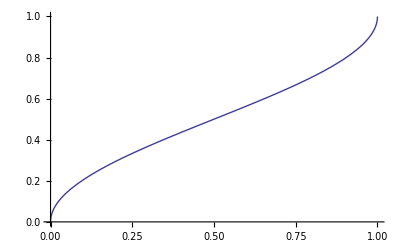

```mathematica
Plot[f[1,x],{x,0,1}]
```

```mathematica
f[t_,x_]:=2/π ArcSin[√(x/t)]
```

```mathematica
Integrate[1-f[t,x],{x,0,t}]
```

$Aborted

```mathematica
Simplify[D[1/(√(a(a+b))),b]]
```

-a/(2 (a (a+b))^(3/2))

```mathematica
Simplify[-a/(2 (a (a+b))^(3/2))/.b->0]
```

-1/(2 a^2)

```mathematica
Series[Abs[x]^2,{x,0,3}]
```

Abs[x]^2

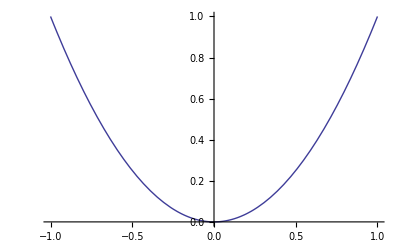

```mathematica
Plot[Abs[x]^2,{x,-1,1}]
```

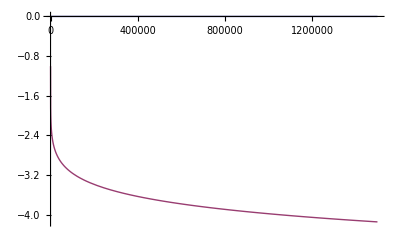

```mathematica
Plot[{0Log[x],-x^.1},{x,1,1500000}]
```

```mathematica
Limit[x^.1,{x-> ∞}]
```

{∞}

```mathematica
Integrate[w^2(2(2m-w))/(t Sqrt[2π t])Exp[(-(2m-w)^2)/(2 t)],{w,-∞,m}]
```

```mathematica
Integrate[(ⅇ^(-m^2/(2 t)) √(2/π) (m^2+2 t))/(√t)-4 m Erfc[m/(√2 √t)],{m,0,1}]
```

-2+ⅇ^(-1/(2 t)) √(2/π) √t+(2+t) Erf[1/(√2 √t)]

```mathematica
Integrate[w^2(2(2m-w))/(t Sqrt[2π t])Exp[(-(2m-w)^2)/(2 t)],{w,-∞,1},{m,0,1}]
```

ⅇ^(-1/(2 t)) (√(2/π) √t+ⅇ^(1/(2 t)) (-2+(2+t) Erf[1/(√2 √t)]))

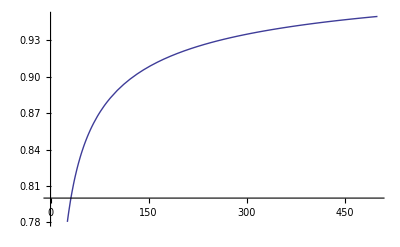

```mathematica
Plot[Erfc[1/(√t)],{t,0,500}]
```